```mathematica
ClearAll["Global`*"];
```

## Exercise 1

## GOE

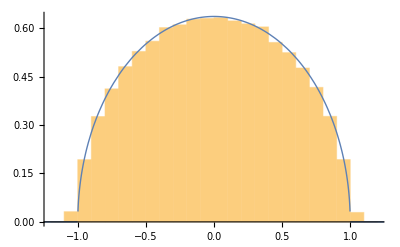

```mathematica
50;
RandomVariate[GaussianOrthogonalMatrixDistribution[1,%],1000];
Show[Histogram[Flatten@Table[Eigenvalues@%[[i]]/√(2%%),{i,1,Length@%}],{0.1},PDF],Plot[PDF[WignerSemicircleDistribution[1],x],{x,-2,2},PlotStyle->{Thick}]]
```

## GUE

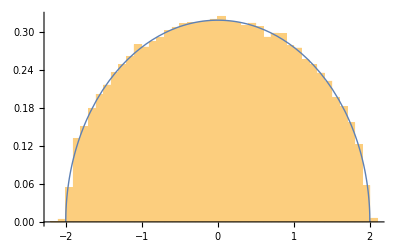

```mathematica
50;
RandomVariate[GaussianUnitaryMatrixDistribution[1,%],1000];
Show[Histogram[Flatten@Table[Eigenvalues@%[[i]]/√(%%),{i,1,Length@%}],{0.1},PDF],Plot[PDF[WignerSemicircleDistribution[2],x],{x,-2,2},PlotStyle->{Thick}]]
```

## Exercise 2

```mathematica
g[n_]:=Module[{distmod,datamod},
distmod=MatrixPropertyDistribution[Table[(#[[i+1]]-#[[i]])&[Sort@Eigenvalues@x],{i,1,Length@x-1}],x\[Distributed]GaussianOrthogonalMatrixDistribution[n]];
datamod=Normalize[Flatten[RandomVariate[distmod,1000]],Mean];
Show[Histogram[datamod,{0.01},PDF,PlotRange->{{0,3},{0,1}},PlotLabel->Style["N="<>ToString@n,20]],Plot[π/2 s ⅇ^(-π/4 s^2),{s,0,3},PlotStyle->{Thick}]]
]
```

```mathematica
Manipulate[g[q],{q,{2,3,4,8,16,32}}]
```

## Exercise 3

```mathematica
h[k_]:=Mean@RandomVariate[MatrixPropertyDistribution[1/50 Tr@MatrixPower[1/(√50)x,k],x\[Distributed]GaussianUnitaryMatrixDistribution[50]],1000];
```

### numerics

```mathematica
Chop[h[#]&/@Table[i,{i,0,10}],10^-10]
```

{1.,0.000192335,0.999985,-0.00128802,2.00531,0.00435261,5.00821,0.00951715,14.0188,0.0447513,42.6958}

### analytics

```mathematica
Series[1/(2)(z-√(z^2-4)),{z,∞,11}](**z*)
```

1/z+(1/z)^3+2/z^5+5/z^7+14/z^9+42/z^11+O[1/z]^12

## Exercise 4

```mathematica
p[j_,n_,λ_]:=1/(π^(1/4)*2^(j/2)*√(j!))(n/(2 σ^2))^(1/4)HermiteH[j,√(n/(2 σ^2))λ]
ρ[λ_,n_]:=1/n ⅇ^(-(n*λ^2)/(2 σ^2))Sum[p[j,n,λ]^2,{j,0,n-1}]/.σ->1
```

```mathematica
Manipulate[Plot[{PDF[WignerSemicircleDistribution[2],x],ρ[x,n]},{x,-3,3},PlotLabel->Style["N="<>ToString@n,20],PlotRange->{All,{0,0.4}}],{n,{1,2,5,10,20}}]
```

## Exercise 5

w mathematice WignerSemicircleDistribution jest proporcjonalny do √(r^2-λ^2), rozkład otrzymywany z GUE jest proporcjonalny do √(4 σ^2-λ^2), natomiast z kumulantów √(4κ-λ^2), czyli κ → σ^2 oraz r →2 √κ

```mathematica
l[κ1_,κ2_,n_]:=Module[{tabmod},
tabmod=Flatten@RandomVariate[MatrixPropertyDistribution[1/(√n)Eigenvalues@(x+y),{x\[Distributed]GaussianUnitaryMatrixDistribution[√κ1,n],y\[Distributed]GaussianUnitaryMatrixDistribution[√κ2,n]}],1000];
Show[Histogram[tabmod,{0.5},PDF],Plot[PDF[WignerSemicircleDistribution[#],x],{x,-#-1,#+1}]&[2 √(κ1+κ2)]]
]
```

```mathematica
Manipulate[l[κ1,κ2,50],{κ1,#},{κ2,#}]&[{1,2,3,5,10}]
```

## Exercise 6

```mathematica
i[n_]:=Module[{datamod},
datamod=Flatten@RandomVariate[MatrixPropertyDistribution[Eigenvalues@(DiagonalMatrix[Table[RandomChoice[{-0.5,0.5}],{i,1,n}]]+x.DiagonalMatrix[Table[RandomChoice[{-0.5,0.5}],{i,1,n}]].x†),x\[Distributed]CircularUnitaryMatrixDistribution[n]],1000];
Show[Histogram[datamod,{0.1},PDF,PlotLabel->Style["N="<>ToString@n,20]],Plot[PDF[ArcSinDistribution[{-1,1}],x],{x,-2,2}]]
]
```

```mathematica
Manipulate[i[n],{n,{1,2,4,8,16,32,64}}]
```

## Exercise 7

## numerics

```mathematica
k[a_,n_]:=Flatten@RandomVariate[MatrixPropertyDistribution[Eigenvalues@((DiagonalMatrix[Table[RandomChoice[{-a,a}],{i,1,n}]]+1/(√n)x)),x\[Distributed]GaussianUnitaryMatrixDistribution[n]],1000]
```

```mathematica
Manipulate[Histogram[k[a,100],{0.1},PDF],{a,{1/2,1,2,10}}]
```

```mathematica
add[a_,n_]:=Module[{matrixmod,amod},
matrixmod=k[a,n];
amod=Table[a,{i,1,Length@matrixmod}];
Transpose@{amod,matrixmod}
]
```

```mathematica
Style[#,20,Thick]&/@{"a","λ","PDF"};
Histogram3D[Flatten[Table[add[i,10],{i,0,4,0.4}],1],{{0.4},{0.25}},PDF,AxesLabel->%,ImageSize->Large]
```

-Graphics3D-

## analytics

```mathematica
sol=Solve[G==1/2(1/(z-a-G)+1/(z+a-G)),G];
```

```mathematica
Manipulate[Plot[Evaluate@(-1/π Limit[Im[G/.sol[[i]]/.{z->λ+ⅈ ϵ,a->b}],ϵ->0,Direction->-1]),{λ,-8,8},PlotRange->{All,{-0.3,0.3}}],{i,{1,2,3}},{b,0,4,0.4}]
```

```mathematica
randtab=Table[{RandomReal[{-8,8}],RandomReal[{0,4}]},{i,0,10000}];
```

```mathematica
(-1/π Limit[Im[G/.sol[[3]]/.{z->λ+ⅈ ϵ}],ϵ->0,Direction->-1]);
tab=Table[{#[[1]],#[[2]],Abs@(%/.{λ->#[[1]],a->#[[2]]})}&[randtab[[i]]],{i,1,Length@randtab}];
```

```mathematica
ListPlot3D[tab,PlotRange->All,Mesh->Full,ImageSize->Large]
```

-Graphics3D-

```mathematica
(-1/π Limit[Im[G/.sol[[3]]/.{z->λ+ⅈ ϵ}],ϵ->0,Direction->-1]);
Plot3D[Abs@%/.{λ->x,a->y},{x,-8,8},{y,0,5}]
```

-Graphics3D-

## Exercise 8

## Real

```mathematica
generateGinibreR[n_,σ_]:=Module[{tabmod1},
tabmod1=RandomVariate[NormalDistribution[0,σ],n^2];
Table[tabmod1[[(i)+(j-1)*n]],{i,1,n},{j,1,n}]]
```

```mathematica
50;
Histogram3D[Flatten@@{Table[ReIm@(1/(√(2%))Eigenvalues@generateGinibreR[%,1]),{i,1000}],1},{{0.1},{0.1}},PDF]
```

-Graphics3D-

```mathematica
w
```

## Complex

```mathematica
complexNormalDistribution[μ_,σ_]:=TransformedDistribution[{x+ⅈ y},{x\[Distributed]NormalDistribution[μ,σ],y\[Distributed]NormalDistribution[μ,σ]}]
```

```mathematica
generateGinibreC[n_,σ_]:=Module[{tabmod1},
tabmod1=Flatten@RandomVariate[complexNormalDistribution[0,σ],2 n^2];
Table[tabmod1[[(i)+(j-1)*n]],{i,1,n},{j,1,n}]]
```

```mathematica
50;
Histogram3D[Flatten@@{Table[ReIm@(1/(√%)Eigenvalues@generateGinibreC[%,1]),{i,1000}],1},{{0.1},{0.1}},PDF]
```

-Graphics3D-

## Exercise 9

```mathematica
generateWishart[NN_,T_,σ_,n_]:=Module[{tabmod1,Xmatrix,Mmatrix},
tabmod1=RandomVariate[NormalDistribution[0,σ],NN*T*n];
Xmatrix=Table[tabmod1[[i+j*NN+nn*(T*NN)]],{nn,0,n-1},{i,1,NN},{j,0,T-1}];
Mmatrix=1/T(#.Transpose@#)&/@Xmatrix;
Show[Histogram[(Eigenvalues@#&/@Mmatrix//Flatten),{0.1},PDF,PlotLabel-> Style@@{"N/T = "<>ToString@(N[NN/T]),25}],Plot[1/(2π NN/T x)√(((1+√(NN/T))^2-x)(x-(1-√(NN/T))^2)),{x,-1,10}]]
]
```

```mathematica
Manipulate[generateWishart[20,t,1,1000],{t,{10,20,40,400}}]
```